```mathematica
mh=1.00794;
mc=12.011;
```

Inputs

```mathematica
r1FName="h.txt";
r2FName="ch4.txt";
```

Point groups

```mathematica
r1PG="";
r2PG="td";
tsPG="c3v";
```

Reactant 1 masses

```mathematica
r1mass={mh};
```

Reactant 1 electronic splitting, eV

```mathematica
r1Elec=Infinity;
```

Reactant 1 g.s. electronic degeneracy

```mathematica
r1g0=2;
```

Reactant 2 masses

```mathematica
r2mass={mc,mh,mh,mh,mh};
```

Reactant 2 electronic splitting, eV

```mathematica
r2Elec=Infinity;
```

Reactant 2 g.s. electronic degeneracy

```mathematica
r2g0=1;
```

TS masses

```mathematica
tsmass={mc,mh,mh,mh,mh,mh};
```

Temperatures (K) of interest

```mathematica
temps=Join[Table[1000/i,{i,1,4,0.1}],{200,250,300,350,400,450,500,600,700,800,1000}];
```

Load packages

```mathematica
Needs["readInTxt`"];
Needs["PartFunc`"];
Needs["RectilProj`"];
Needs["Anharmonicities`"];
SetDirectory[NotebookDirectory[]];
```

Constant parameters

Speed of light, cm/s

```mathematica
ccm=2.997925*^10;
```

a_0 in meters

```mathematica
mpera0=5.29177249*^-11;
```

Planck constant, Js

```mathematica
h=6.6260755*^-34;
```

Hartree in J

```mathematica
Eh=4.359748*^-18;
```

Boltzmann constant, J/K

```mathematica
kb=1.380650*^-23;
```

Da in kg

```mathematica
kgperamu=1.660538922*^-27;
```

Reactant 1 partition functions

```mathematica
r1Data=readInTxtAtom[r1FName,2];
```

```mathematica
r1NonElecQ=nonElecPartAtom[Total[r1mass],temps];
r1ElecQ=r1g0+Exp[-r1Elec*1.602177*^-19/kb/temps];
```

Reactant 2 partition functions

```mathematica
r2Data=readInTxt[r2FName,Length[r2mass],3];
```

```mathematica
r2NonElecQ=nonElecPartMol[r2Data[[1]],r2Data[[2]],r2mass,r2PG,temps];
r2ElecQ=r2g0+Exp[-r2Elec*1.602177*^-19/kb/temps];
```

```mathematica
r2NonElecNonVibQ=nonElecnonVibPartTS[r2Data[[1]],r2mass,r2PG,temps];
```

TS partition functions

```mathematica
tsData=readInTxt["ts.txt",Length[tsmass],3];
```

```mathematica
tsNonVibNonElecQ=nonElecnonVibPartTS[tsData[[1]],tsmass,tsPG,temps];
tsElecQ=2;
```

```mathematica
tsNonElecQ=nonElecPartMol[tsData[[1]],tsData[[2]],tsmass,tsPG,temps];
```

Vibrationally adiabatic TST barrier height, a.u.

```mathematica
r2Freq=Delete[RectilProj[r2Data[[1]],r2Data[[2]],r2mass,{{1,2},{2,3}},"pre"][[1]],{{-1},{-2},{-3},{-4},{-5},{-6}}];
```

SC barrier height, a.u.

```mathematica
G0=0.00001874495246031809;
```

```mathematica
CH4G0=0.00013112120672859816;
```

```mathematica
CH4states=Import["CH4_States_4.txt","CSV"];
```

```mathematica
QvibCH4=Sum[CH4states[[i,2]]Exp[-(CH4states[[i,1]]-(CH4states[[1,1]]+CH4G0))*Eh/kb/temps],{i,Length[CH4states]}];
```

```mathematica
ΔVo=tsData[[4,2]]-r1Data[[2]]-r2Data[[4,2]]+G0-CH4states[[1,1]]-CH4G0
```

-0.0211926

```mathematica
ch3Data=readInTxt["ch3.txt",4,3];
```

```mathematica
ch3Freq=Delete[RectilProj[ch3Data[[1]],ch3Data[[2]],{mc,mh,mh,mh},{{1,2},{2,3}},"pre"][[1]],{{-1},{-2},{-3},{-4},{-5},{-6}}];
```

```mathematica
h2Data=readInTxt["h21.txt",2,3];
```

```mathematica
h2Freq=RectilProj[h2Data[[1]],h2Data[[2]],{mh,mh},{{1,2},{1,2}},"pre"][[1,1]];
```

```mathematica
ΔVr=tsData[[4,2]]-ch3Data[[4,2]]-h2Data[[4,2]]+G0-(Total[ch3Freq]+h2Freq)/2*4.556355*^-6
```

-0.0219321

```mathematica
CRP=Import["CRP_W.txt","CSV"];
```

```mathematica
Estep=CRP[[2,1]]-CRP[[1,1]];
```

```mathematica
weights=Table[CRP[[i,2]]*Exp[(-(CRP[[i,1]])*Eh)/(kb temps)],{i,Length[CRP]}];
```

```mathematica
kWag=tsNonVibNonElecQ tsElecQ/(h r1NonElecQ r1ElecQ r2NonElecNonVibQ r2ElecQ QvibCH4)Sum[0.5 (weights[[i]]+weights[[i+1]]),{i,Length[CRP]-1}]*Estep*Eh*100^3;
```

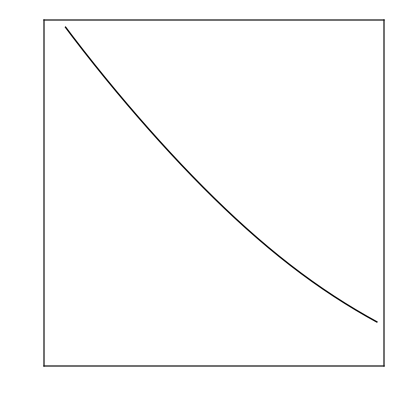

```mathematica
ListPlot[{Transpose[{1000/temps[[1;;31]],Log10[kWag[[1;;31]]]}]},Joined->True,PlotStyle->{{Black}},PlotRange->{{1,4},{-20,-13}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->{Table[{i,"",{If[Mod[i-2,1]==0,0.02,0.01],0}},{i,1,4,0.2}],Table[{i,"",{If[Mod[i+20,2]==0,0.02,0.01],0}},{i,-20,-13,0.5}],{{1000/750,"",{0.02,0}},{1000/500,"",{0.02,0}},{1000/300,"",{0.02,0}},{4,"",{0.02,0}}},Table[{i,"",{If[Mod[i+20,2]==0,0.02,0.01],0}},{i,-20,-13,0.5}]}]
```

```mathematica
kWag[[32;;42]]
```

{5.88823×10^-21,6.02915×10^-20,5.64494×10^-19,4.28986×10^-18,2.47995×10^-17,1.10082×10^-16,3.90103×10^-16,2.92305×10^-15,1.34457×10^-14,4.45333×10^-14,2.61002×10^-13}